##### Code

```mathematica
plotTree=Function[{labels},
Module[{coords},
coords = {{1,2},{2.5,3},{2,2},{3,2},{4,2},{1,0},{2.5,0},{4,0}};
TreePlot[{{2->1,"2"},{3->1,"1"},{4->1,"-3"},{5->1,"-2"},
{6->3,"1"},{6->4,"2"},{6->5,"3"},
{7->3,"-3"},{7->4,"2"},{7->5,"1"},
{8->3,"1"},{8->4,"-2"},{8->5,"1"}},
VertexLabeling->True,DirectedEdges->True,VertexRenderingFunction->(Text[Panel[Style[labels[[#2]],Small]],#1]&),
VertexCoordinateRules-> coords]]];
perceptronPlot=Module[{labels},
labels={"g[∑_(i = 0)^3 w_i X_i]","X_0=1","X_1","X_2"};
TreePlot[{{2->1,"w_0"}, {3->1,"w_1"}, {4->1,"w_1"}},VertexLabeling->True,DirectedEdges->True,VertexRenderingFunction->(Text[Panel[Style[labels[[#2]],Medium]],#1]&)]];

plt =Module[{labels, coords},labels={"out(x)=g[∑_(i = 0)^3 u_i Z_i]","Z_0=1","Z_1=g[∑_(i = 0)^2 w_i^1X_i]","Z_2=g[∑_(i = 0)^2 w_i^2X_i]","Z_3=g[∑_(i = 0)^2 w_i^3X_i]","X_0=1","X_2","X_1"};
coords = {{1,2},{2.5,3},{2,2},{3,2},{4,2},{1,0},{2.5,0},{4,0}};

TreePlot[{{2->1,"u_0"},{3->1,"u_1"},{4->1,"u_2"},{5->1,"u_3"},
{6->3,"w_0^1"},{6->4,"w_1^1"},{6->5,"w_2^1"},
{7->3,"w_0^2"},{7->4,"w_1^2"},{7->5,"w_2^2"},
{8->3,"w_0^3"},{8->4,"w_1^3"},{8->5,"w_2^3"}},
VertexLabeling->True,DirectedEdges->True,VertexRenderingFunction->(Text[Panel[Style[labels[[#2]],Small]],#1]&),
VertexCoordinateRules->coords]
];
dynamicDemo =DynamicModule[{w10,w11,w12,w20,w21,w22,w30,w31,w32,u0,u1,u2,g},
r={-3,3};
g=Function[x,1/(1+Exp[-x])];
Grid[{
{MatrixForm[{{Slider[Dynamic[w10],r],Slider[Dynamic[w11],r],Slider[Dynamic[w12],r]},
{Slider[Dynamic[w20],r],Slider[Dynamic[w21],r],Slider[Dynamic[w22],r]},
{Slider[Dynamic[w30],r],Slider[Dynamic[w31],r],Slider[Dynamic[w32],r]}}]},
{MatrixForm[{{Slider[Dynamic[u0],r],Slider[Dynamic[u1],r],Slider[Dynamic[u2],r]}}]},
{Dynamic[
Plot3D[
g[Total[Flatten[
{{u0,u1,u2}} . g[{{w10,w11,w12},{w20,w21,w22},{w30,w31,w32}} .{{1},{a},{b}}]]
]],
{a,-10,10},{b,-10,10}]
]}}]
];
```

# Neural Networks

Carlos Morato, PhD.

We are going to go through Neural Networks and review the process of back propagation.

Experimental Mathematica based presentation.

## Single Perceptron

##### The Perceptron

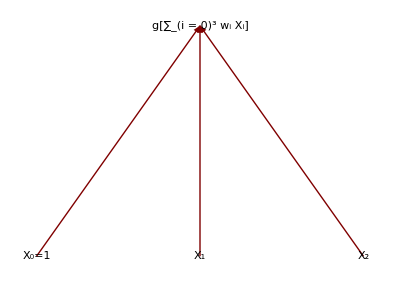

```mathematica
perceptronPlot
```

##### There are several parts

Link Function g[u]

Weights w_i

A bias term X_0

## Link Function

g[x]=1/(1+ⅇ^-x)

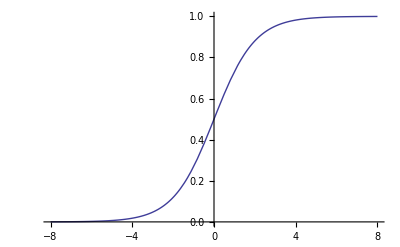

```mathematica
g=Function[x,1/(1+Exp[-x])];
Plot[g[x],{x,-8,8}]
```

## Demo

```mathematica
Manipulate[
g=Function[x,1/(1+Exp[-x])];
Plot3D[ g[w0 + w1 x1 + w2 x2],{x1,-3,3},{x2,-3,3}],
{{w0,0},-3,3},{{w1,2},-3,3},{{w2,-2},-3,3}
]
```

## Neural Network with Multiple Hidden Layers

##### Lets Consider what this network looks like

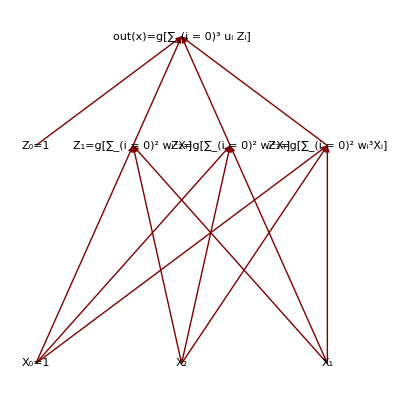

```mathematica
plt
```

##### Matlab Style Forward Propagation

Lets define a matrix Was:

W=(w_0^1 | w_1^1 | w_2^1
w_0^2 | w_1^2 | w_2^2
w_0^3 | w_1^3 | w_2^3)

We can multiply this matrix by X where we have added a 1

W·(1
X_1
X_2)=(w_0^1 | w_1^1 | w_2^1
w_0^2 | w_1^2 | w_2^2
w_0^3 | w_1^3 | w_2^3)·(1
X_2
X_3)=(w_0^1+w_1^1 X_1+w_2^1 X_2
w_0^2+w_1^2 X_1+w_2^2 X_2
w_0^3+w_1^3 X_1+w_2^3 X_2)

Lets define function application as element wise.  Then we obtain:

g[W·(1
X_2
X_3)]=(g[w_0^1+w_1^1 X_1+w_2^1 X_2]
g[w_0^2+w_1^2 X_1+w_2^2 X_2]
g[w_0^3+w_1^3 X_1+w_2^3 X_2])=(Z_1
Z_2
Z_3)

We can then prepend a 1 to the result to obtain:

out(X)=g[(u_0 | u_1 | u_2 | u_3)·(1
Z_1
Z_2
Z_3)]=g[u_0+∑_(i=1)^3 u_i Z_i]

## Forward Propagation (Example) #1

##### What is the value of Z_1

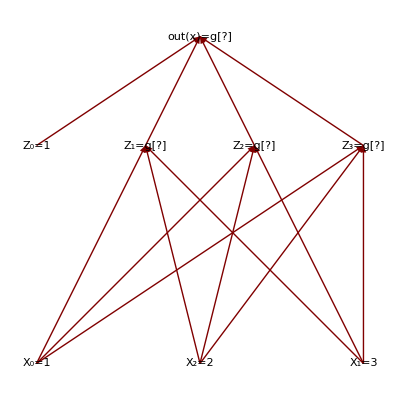

```mathematica
plotTree[{"out(x)=g[?]","Z_0=1","Z_1=g[?]","Z_2=g[?]","Z_3=g[?]","X_0=1","X_2=2","X_1=3"}]
```

## What is the value of Z_2?

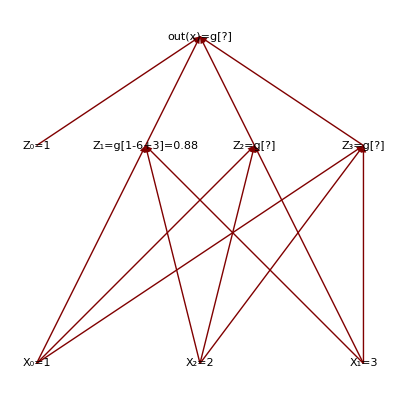

```mathematica
plotTree[{"out(x)=g[?]","Z_0=1","Z_1=g[1-6+3]=0.88","Z_2=g[?]","Z_3=g[?]","X_0=1","X_2=2","X_1=3"}]
```

## What is the value of Z_3?

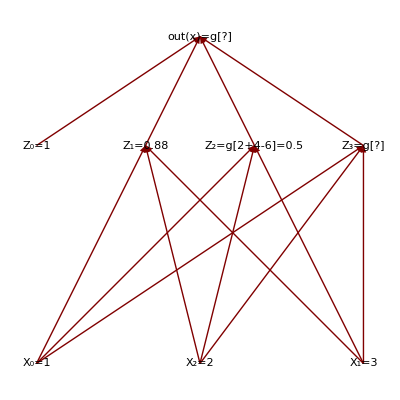

```mathematica
plotTree[{"out(x)=g[?]","Z_0=1","Z_1=0.88","Z_2=g[2+4-6]=0.5","Z_3=g[?]","X_0=1","X_2=2","X_1=3"}]
```

## What is the value of out(X)?

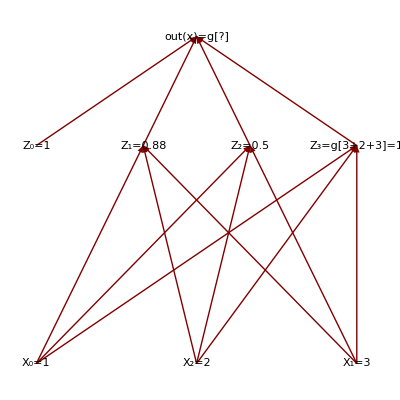

```mathematica
plotTree[{"out(x)=g[?]","Z_0=1","Z_1=0.88","Z_2=0.5","Z_3=g[3+2+3]=1","X_0=1","X_2=2","X_1=3"}]
```

## Done!

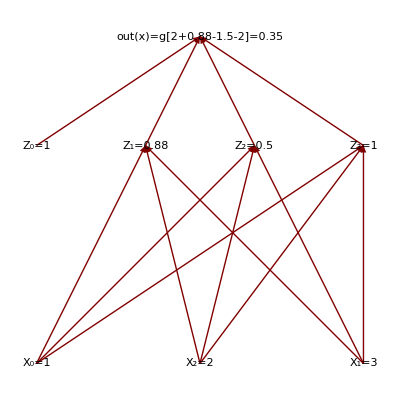

```mathematica
plotTree[{"out(x)=g[2+0.88-1.5-2]=0.35","Z_0=1","Z_1=0.88","Z_2=0.5","Z_3=1","X_0=1","X_2=2","X_1=3"}]
```

## Demo

```mathematica
dynamicDemo
```

## Generalized Back Propagation

```mathematica
plt
```

-Graphics-

Suppose we want to find the best model out(x;U,W) with respect to the parameters W and U.  How can we quantify best? Lets considered mean squared error.

E=∑_(i=1)^n (out(X_i)-Y_i)^2

There are many ways to do this.  One of the most common (and least effective) methods is to use gradient descent. This corresponds to the update rule:

u_i^(t+1)⟵u_i^(t)-η (∂E)/(∂u_i)| 
u_i^(t)

w_ij^(t+1)⟵w_ij^(t)-η (∂E)/(∂w_ij)| 
w_ij^(t)

Recall we have the following graph:

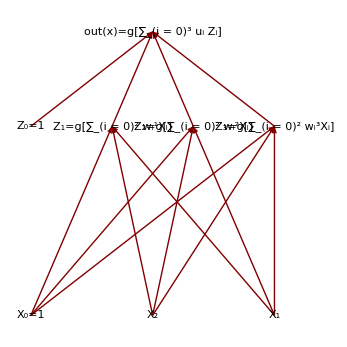

```mathematica
plt
```

Lets first derive the update rule for U:

E=(out(X)-Y)^2

Taking the derivative we get (stuck?):

(∂E)/(∂u_k)=∂/(∂u_k)(out(X)-Y)^2

Applying the infamous chain rule:

∂/(∂x)f(g(x))=(∂/(∂u)f(u)| 
u=g(x))(∂/(∂x)g(x))

(∂E)/(∂u_k)=(2(out(X)-Y_i))_(⏟_(∂/(∂x)x^2= 2x))(∂/(∂u_k)out(X))

∂/(∂x)f(g(x)) = f'(g(x)) g'(x)

Now we need to take the derivative of the neural network.  Lets first replace out with the function from the top perceptron

(∂E)/(∂u_k)=2(out(X)-Y)(∂/(∂u_k)g[∑_(i=0)^3 u_i Z_i])

Chain rule again

(∂E)/(∂u_k)=2(out(X)-Y)g'[∑_(i=0)^3 u_i Z_i](∑_(i=0)^3 ∂/(∂u_k)u_i Z_i)

We know that only one term in the Z_i sum will remain and that is Z_(i=k)

(∂E)/(∂u_k)=2(out(X)-Y)g'[∑_(i=0)^3 u_i Z_i] Z_k

Done that’s it!!!  Sort of.  Lets look at the derivative of g[x]=1/(1-Exp[-x])

g'[x]=∂/(∂x)(1+Exp[-x])^-1

g'[x]=-(1+Exp[-x])^-2∂/(∂x)(1+Exp[-x])

g'[x]=-(1+Exp[-x])^-2(∂/(∂x)1+∂/(∂x)Exp[-x])

g'[x]=-(1+Exp[-x])^-2(0+Exp[-x]∂/(∂x)(-x))

g'[x]=-(1+Exp[-x])^-2(0-Exp[-x])

g'[x]=(1+Exp[-x])^-2 Exp[-x]

With some manipulation we get:

g'[x]=Exp[-x]/(1+Exp[-x])1/(1+Exp[-x])

g'[x]=Exp[-x]/(1+Exp[-x])g[x]

g'[x]=(1+Exp[-x]-1)/(1+Exp[-x])g[x]

g'[x]=((1+Exp[-x])/(1+Exp[-x])+-1/(1+Exp[-x]))g[x]

g'[x]=(1-1/(1+Exp[-x]))g[x]

g'[x]=(1-g[x])g[x]

Recall that we earlier had:

(∂E)/(∂u_k)=2(out(X)-Y)g'[∑_(i=0)^3 u_i Z_i]Z_k

we can make a simple substitution to get:

(∂E)/(∂u_k)=2(out(X)-Y)(1-g[∑_(i=0)^3 u_i Z_i])g[∑_(i=0)^3 u_i Z_i]Z_k

(∂E)/(∂u_k)=2(out(X)-Y)(1-out(X))out(X)Z_k

```mathematica
plt
```

-Graphics-

## Gradient of W

That wasn't too bad.  How about the next layer.  We again start with:

E=(out(X)-Y)^2

Taking the derivative with respect to w_k^r (and applying the chain rule)

(∂E)/(∂w_k^r)=(∂E)/(∂out(X))(∂out(X))/(∂w_k^r)=2(out(X)-Y)∂/(∂w_k^r)out(X)

Expanding out we get:

(∂E)/(∂w_k^r)=2(out(X)-Y)∂/(∂w_k^r)g[∑_(i=0)^3 u_i Z_i]

Chain rule:

(∂E)/(∂w_k^r)=2(out(X)-Y)(g'[∑_(i=0)^3 u_i Z_i])(∑_(i=0)^3 ∂/(∂w_k^r) u_i Z_i)

Recall that g'[x]=(1-g[x])g[x]

(∂E)/(∂w_k^r)=2(out(X)-Y)(1-out(X))out(X)(∑_(i=0)^3 ∂/(∂w_k^r) u_i Z_i)

Remember that each of the Z_i is connected to all the perceptrons from the lower level so we must take the derivative of each.

(∂E)/(∂w_k^r)=2(out(X)-Y)(1-out(X))out(X)(∑_(i=0)^3 u_i∂/(∂w_k^r)Z_i)

Which becomes:

(∂E)/(∂w_k^r)=2(out(X)-Y)(1-out(X))out(X)(∑_(i=0)^3 u_i∂/(∂w_k^r)g[∑_(s=0)^3 w_s^i X_s])

Another application of the chain rule:

(∂E)/(∂w_k^r)=2(out(X)-Y)(1-out(X))out(X)∑_(i=0)^3 u_i g'[∑_(s=0)^3 w_s^i X_s]∂/(∂w_k^r)∑_(s=0)^3 w_s^i X_s

Taking the final derivative we have:

(∂E)/(∂w_k^r)=2(out(X)-Y)(1-out(X))out(X)(∑_(i=0)^3 u_i (1-Z_i)(Z_i))X_k

## Why is it called back propagation?

Lets look at the following two equations:

(∂E)/(∂u_k)=2(out(X)-Y)(1-out(X))out(X)Z_k

(∂E)/(∂w_k^r)=2(out(X)-Y)(1-out(X))out(X)∑_(i=0)^3 u_i (1-Z_i)(Z_i)X_k

```mathematica
plt
```

-Graphics-

We propagate the derivative information backwards to the inputs:

(∂E)/(∂u_k)=(2(out(X)-Y)(1-out(X))out(X))Z_k

(∂E)/(∂w_k^r)=(2(out(X)-Y)(1-out(X))out(X))∑_(i=0)^3 u_i (1-Z_i)(Z_i)X_k

(∂E)/(∂w_k^r)=((2(out(X)-Y)(1-out(X))out(X))∑_(i=0)^3 u_i (1-Z_i)(Z_i))X_k

## Questions?

◀     |     ▶

##### Any feedback about Mathematica style presentations is welcome.